# Assignment 7 Mathematica for Research Azam Jainullabudin Mohamed

### Analytically solving equations

Find the cube roots of 1 (three of them) by writing out a suitable equation to solve and then using Solve. Print out approximate numerical values. Check that you’ve found the right values by substituting back into the equation you solved.

```mathematica
a =N[Solve[x^3 ==-1,x]]
```

{{x→-1.},{x→0.5+0.866025 ⅈ},{x→0.5-0.866025 ⅈ}}

```mathematica
Round[x^3 ] == -1 /. a
```

{True,True,True}

Find the range of values for x for which x^2+3x>0. Hint: look up the Reduce function.

```mathematica
Reduce[x^2 + 3 x ==0, x]
```

x==-3||x==0

Compare the solution of Cos[x]=0 using Solve and Reduce.

```mathematica
Clear[x];
```

```mathematica
sol1 = Solve[Cos[x] == 0, x]
```

{{x→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
sol2 = Reduce[Cos[x] == 0, x]
```

C[1]∈ℤ&&(x==-π/2+2 π C[1]||x==π/2+2 π C[1])

Solve is used mostly for finding the generic solutions to an equation, whereas Reduce is used for maintaining all solutions after reducing the equations.

Consider the 5th order polynomial a x^5+b x^4+c x^3+d x^2+e x+f. Make a Manipulate that finds all 5 roots (solves for x) in the complex plane for this polynomial (choose slider controls for each coefficient a, b, c, d, e and f with small ranges [-2,2] for each). The result should be a list of 5 complex numbers corresponding to the 5 roots. By using the real part of the solutions for x coordinates and the imaginary part for y coordinates, use ListPlot to plots the roots. Fix the plot range to {{-2,2},{-2,2}} so that its possible to see how the roots move.

```mathematica
sol = Solve[a*x^5 + b*x^4 +c*x^3 + d*x^2+e*x+f==0, x]
```

{{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,1]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,2]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,3]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,4]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,5]}}

```mathematica
Manipulate[ListPlot[ReIm[x/.Solve[a*x^5 + b*x^4 +c*x^3 + d*x^2+e*x+f==0, x]],PlotRange->{{-2,2}, {-2,2}}], {a,-2,2}, {b,-2,2}, {c,-2,2}, {d,-2,2}, {e,-2,2},{f,-2,2}]
```

Create a polynomial with 5 real roots (Hint: a polynomial crosses the axis and has a root at x=x_0 iff it has a factor (x-x_0).) and use Solve to find the roots. Verify that your polynomial has 5 roots by plotting it and checking it crosses the axis 5 times.

```mathematica
f = x^5+x^4-43*x^3-25*x^2+378*x+360
```

360+378 x-25 x^2-43 x^3+x^4+x^5

```mathematica
Solve[f==0,x]
```

{{x→-6},{x→-3},{x→-1},{x→4},{x→5}}

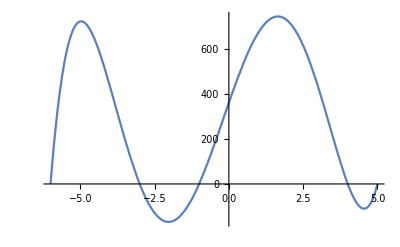

```mathematica
Plot[f,{x,-6,5}]
```

### Numerically solving

Use NSolve to find all 5 roots of the polynomial from the previous question.

```mathematica
Clear[x];
val = 2 x^5 + 3 x^4 +4 x^3 + 5 x^2+6 x+7==0;
```

```mathematica
NSolve[val]
```

{{x→-1.30029},{x→-0.672775-1.10671 ⅈ},{x→-0.672775+1.10671 ⅈ},{x→0.572918-1.12979 ⅈ},{x→0.572918+1.12979 ⅈ}}

The product log function is defined to be to solution for x≥-1/ⅇ of the equation y=x ⅇ^x. Define a function that, given a y value, uses FindRoot to determine an x value.

```mathematica
Clear[x,y]
```

```mathematica
y = x * ⅇ^x;
```

```mathematica
func[y_] :=x/.FindRoot[y == x*ⅇ^x, {x, -1/ⅇ}];
```

```mathematica
func[2.5]
```

0.958586

```mathematica
ProductLog[2.5]
```

0.958586

Plot your function from the previous question and compare against a plot of the built-in ProductLog function. In this case you could have just used ProductLog, but in general there may not be an exact solution and the FindRoot method can be useful.

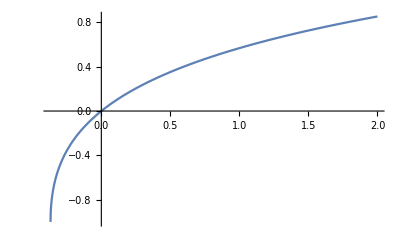

```mathematica
Plot[func[x], {x, -1/E,2}]
```

```mathematica
Plot[ProductLog[y],{y, -1/ⅇ,2}]
```

-Graphics-

In the previous question you could have just used ProductLog, but in general there may not be an exact solution and the FindRoot method can be useful. Consider the implicit equation u-π==w^-1(1-Cos[w])-1/2 w. In this case Reduce and Solve can’t find a solution for w as a function of u. Write a function which uses FindRoot to numerically solve for w for a given numeric value of u. (Hint: use w=1 as a starting guess in FindRoot)

```mathematica
numeric[u_]:= w /.FindRoot[u-π == w^-1(1-Cos[w]) - w * 1/2, {w,1}];
```

```mathematica
numeric[-π]
```

12.5664

Plot the function from the previous question for -2π≤u≤4π

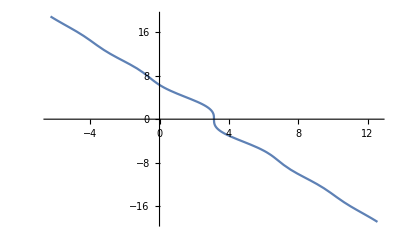

```mathematica
Plot[numeric[u], {u, -2π, 4π}]
```